```mathematica
urlCovid19="https://pomber.github.io/covid19/timeseries.json"
```

https://pomber.github.io/covid19/timeseries.json

```mathematica
cov19=Import[urlCovid19];
```

```mathematica
as19=Association[cov19]
```

<|Afghanistan→{{date→2020-1-22,confirmed→0,deaths→0,recovered→0},{date→2020-1-23,confirmed→0,deaths→0,recovered→0},826,{date→2022-4-29,confirmed→178873,deaths→7683,recovered→0},{date→2022-4-30,confirmed→178879,deaths→7683,recovered→0}},196,Zimbabwe→1|>
 |  |  |  |

```mathematica
asas19=Map[Association,as19,{3}]
```

<|Afghanistan→{{<|date→2020-1-22|>,<|confirmed→0|>,<|deaths→0|>,<|recovered→0|>},828,{<|date→2022-4-30|>,<|confirmed→178879|>,<|deaths→7683|>,<|recovered→0|>}},196,Zimbabwe→{{<|date→2020-1-22|>,<|confirmed→0|>,<|deaths→0|>,<|recovered→0|>},828,{1}}|>
 |  |  |  |

```mathematica
asas19["Japan"]
```

{{<|date→2020-1-22|>,<|confirmed→2|>,<|deaths→0|>,<|recovered→0|>},{<|date→2020-1-23|>,<|confirmed→2|>,<|deaths→0|>,<|recovered→0|>},826,{<|date→2022-4-29|>,<|confirmed→7846274|>,<|deaths→29553|>,<|recovered→0|>},{<|date→2022-4-30|>,<|confirmed→7871253|>,<|deaths→29567|>,<|recovered→0|>}}
 |  |  |  |

```mathematica
ts["Japan","confirmed"]=Map[{AbsoluteTime[#[[1]]["date"]],#[[2]]["confirmed"]}&,asas19["Japan"]];
```

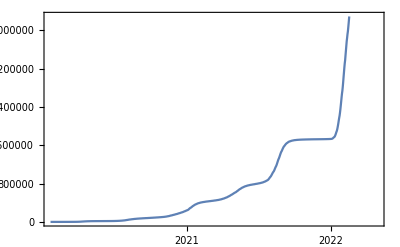

```mathematica
DateListPlot[ts["Japan","confirmed"]]
```

```mathematica
its["Japan","confirmed"]=Interpolation[ts["Japan","confirmed"]]
```

InterpolatingFunction[…]

```mathematica
startTime["Japan"]=AbsoluteTime[asas19["Japan"][[1]][[1]]["date"]]
```

3788640000

```mathematica
endTime["Japan"]=AbsoluteTime[asas19["Japan"][[-1]][[1]]["date"]]
```

3860265600

```mathematica
days["Japan"]=(endTime["Japan"]-startTime["Japan"])/60/60/24
```

829

```mathematica
count["Japan","confirmed"]=Table[its["Japan","confirmed"][t],{t,startTime["Japan"],endTime["Japan"],60*60*24}];
```

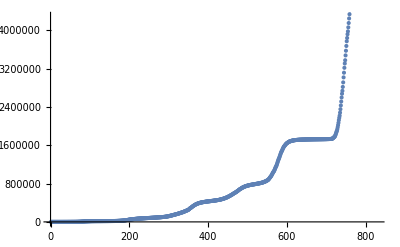

```mathematica
ListPlot[count["Japan","confirmed"]]
```

```mathematica
fou["Japan","confirmed"]=Fourier[count["Japan","confirmed"]];
```

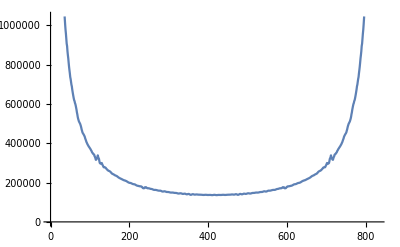

```mathematica
ListLinePlot[fou["Japan","confirmed"]//Abs]
```